```mathematica
NA = 6.0221367 10^23;
Dtot=10^-11;
kf=10^6 / NA;
kd=10^3;
sigma=1 10^-7;
kD=4*Pi*sigma*Dtot;
h=(1+kf/kD)*Sqrt[Dtot]/sigma;
a=kd*Sqrt[Dtot]/sigma;
r0=sigma;
tau = sigma^2 / Dtot;
t= tau 10^-1;
maxr = 4.5 Sqrt[ 6 Dtot t];
```

```mathematica
ciccio=N[Solve[{x+y+z==h, x*y+y*z+x*z==kd,x*y*z==a},{x,y,z}]];
alpha=ciccio[[1,1,2]];
beta = ciccio[[1,2,2]];
gamma=ciccio[[1,3,2]];
```

```mathematica
W[x_,y_]:=Exp[2*x*y+y^2]*Erfc[x+y];
frac[x_,y_,z_]:=(x*(z+x)*(x+y))/((z-x)*(x-y));
coeff[r_]:=1/(4*Pi*r*r0*Sqrt[Dtot]);
term1[r_]:=1/Sqrt[4*Pi*t]*(Exp[-(r-r0)^2/(4*Dtot*t)]+Exp[-(r+r0-2*sigma)^2/(4*Dtot*t)]);
term2[r_]:=frac[alpha,beta,gamma]*W[(r+r0-2*sigma)/(Sqrt[4*Dtot*t]),alpha*Sqrt[t]];
term3[r_]:=frac[beta,gamma,alpha]*W[(r+r0-2*sigma)/(Sqrt[4*Dtot*t]),beta*Sqrt[t]];
term4[r_]:=frac[gamma,alpha,beta]*W[(r+r0-2*sigma)/(Sqrt[4*Dtot*t]),gamma*Sqrt[t]];
```

```mathematica
f[r_]:=4*Pi*r^2*Re[coeff[r]*(term1[r]+term2[r]+term3[r]+term4[r])]
```

c = N[Integrate[f[r], {r, 1, Infinity}]]

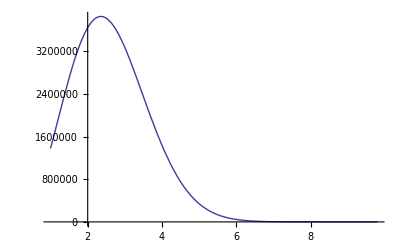

```mathematica
Plot[f[r], {r,sigma,maxr}]
```

```mathematica
out=Table[{r,f[r]},{r,sigma,maxr,(maxr - sigma) / 100}] // N
```

{{1.×10^-7,1.37935×10^6},{1.08798×10^-7,1.61106×10^6},{1.17596×10^-7,1.8476×10^6},{1.26394×10^-7,2.08519×10^6},{1.35192×10^-7,2.32006×10^6},{1.4399×10^-7,2.54849×10^6},{1.52788×10^-7,2.76692×10^6},{1.61586×10^-7,2.97201×10^6},{1.70384×10^-7,3.16073×10^6},{1.79182×10^-7,3.33039×10^6},{1.8798×10^-7,3.4787×10^6},{1.96778×10^-7,3.60381×10^6},{2.05576×10^-7,3.70431×10^6},{2.14373×10^-7,3.77931×10^6},{2.23171×10^-7,3.82834×10^6},{2.31969×10^-7,3.85144×10^6},{2.40767×10^-7,3.84906×10^6},{2.49565×10^-7,3.82208×10^6},{2.58363×10^-7,3.77173×10^6},{2.67161×10^-7,3.69959×10^6},{2.75959×10^-7,3.60748×10^6},{2.84757×10^-7,3.49745×10^6},{2.93555×10^-7,3.37173×10^6},{3.02353×10^-7,3.23263×10^6},{3.11151×10^-7,3.08252×10^6},{3.19949×10^-7,2.92378×10^6},{3.28747×10^-7,2.75873×10^6},{3.37545×10^-7,2.5896×10^6},{3.46343×10^-7,2.41852×10^6},{3.55141×10^-7,2.24743×10^6},{3.63939×10^-7,2.07812×10^6},{3.72737×10^-7,1.91217×10^6},{3.81535×10^-7,1.75097×10^6},{3.90333×10^-7,1.59569×10^6},{3.99131×10^-7,1.44728×10^6},{4.07929×10^-7,1.30651×10^6},{4.16727×10^-7,1.17394×10^6},{4.25524×10^-7,1.04994×10^6},{4.34322×10^-7,934731.},{4.4312×10^-7,828374.},{4.51918×10^-7,730797.},{4.60716×10^-7,641814.},{4.69514×10^-7,561146.},{4.78312×10^-7,488436.},{4.8711×10^-7,423267.},{4.95908×10^-7,365180.},{5.04706×10^-7,313685.},{5.13504×10^-7,268277.},{5.22302×10^-7,228446.},{5.311×10^-7,193688.},{5.39898×10^-7,163511.},{5.48696×10^-7,137444.},{5.57494×10^-7,115038.},{5.66292×10^-7,95875.3},{5.7509×10^-7,79565.1},{5.83888×10^-7,65749.9},{5.92686×10^-7,54104.2},{6.01484×10^-7,44333.8},{6.10282×10^-7,36175.3},{6.1908×10^-7,29394.5},{6.27878×10^-7,23785.},{6.36675×10^-7,19165.8},{6.45473×10^-7,15379.4},{6.54271×10^-7,12289.9},{6.63069×10^-7,9780.32},{6.71867×10^-7,7751.05},{6.80665×10^-7,6117.48},{6.89463×10^-7,4808.32},{6.98261×10^-7,3763.79},{7.07059×10^-7,2934.08},{7.15857×10^-7,2277.9},{7.24655×10^-7,1761.24},{7.33453×10^-7,1356.21},{7.42251×10^-7,1040.06},{7.51049×10^-7,794.361},{7.59847×10^-7,604.238},{7.68645×10^-7,457.752},{7.77443×10^-7,345.372},{7.86241×10^-7,259.527},{7.95039×10^-7,194.229},{8.03837×10^-7,144.773},{8.12635×10^-7,107.474},{8.21433×10^-7,79.4632},{8.30231×10^-7,58.5159},{8.39029×10^-7,42.917},{8.47827×10^-7,31.3498},{8.56624×10^-7,22.8082},{8.65422×10^-7,16.5273},{8.7422×10^-7,11.9279},{8.83018×10^-7,8.57402},{8.91816×10^-7,6.13849},{9.00614×10^-7,4.37721},{9.09412×10^-7,3.1088},{9.1821×10^-7,2.19912},{9.27008×10^-7,1.54942},{9.35806×10^-7,1.0873},{9.44604×10^-7,0.759974},{9.53402×10^-7,0.529069},{9.622×10^-7,0.366853},{9.70998×10^-7,0.253362},{9.79796×10^-7,0.174284}}

```mathematica
Export["p_rev.-1.tsv",out]
```

p_rev.0.tsv